```mathematica
Clear["Global`*"];

(* Exploitation parameter *)
beta = {beta1,beta2}; 
(* Learning rate *)
alpha = {alpha1,alpha2};
(* Discount factor *)
gamma = {gamma1,gamma2};
(* Prosocial factor *)
delta = {delta1,delta2};

(* Reward matrix *)
(* r_i,a1,a2 *)
RM = {{{r111,r112},{r121,r122}},{{r211,r212},{r221,r222}}};
(* Symmetric *)
(*RM = {{{r11,r12},{r21,r22}},{{r11,r21},{r12,r22}}};*)

(* Q-table *)
(* q_i,a *)
Q = {{q11,q12},{q21,q22}};

(* Behavior profiles as functions of Q *)
(* x_i,a *)
Z=Total[Exp[beta*Q],{2}];
XQ = Exp[beta*Q]/Z;

(* Behavior profiles as independent variables *)
(* x_i,a *)
X = {{X11,X12},{X21,X22}};

(* Q as functions of X *)
QX = Log[X]/beta ;
(*QX = QX + Log[Z]*)
QXrule=Thread[Flatten[Q] -> Flatten[QX]];

(* Joint behavioral profile *)
(* Xvec_a1,a2 *)
Xs = Times @@{{{X11,X11},{X12,X12}},{{X21,X22},{X21,X22}}};
```

```mathematica
(* Deterministic limit (Eq. 17) ------------------------------------------------------------*)

Clear[alpha1,alpha2,beta1,beta2,gamma1,gamma2];
(* a'<R>_i,a (Given a_i, average over other agent's action a_i' to get average R_i) *)
Risa =ConstantArray[0,{2,2}];
(* i's = indices, j's = summation *)
For[i1=1,i1<3,i1++, (*i*)
For[i2=1,i2<3,i2++,(*a*)
For[j1=1,j1<3,j1++,(*a'*)
(* Other agent's id *)
If[i1==1,iother=2;a1=i2;a2=j1;,iother=1;a1=j1;a2=i2;];
(* Boltzmann exploration *)
Prob=XQ[[iother,j1]];
(* Epsilon greedy *)
(*If[j1==1,Prob=eps1[Q[[iother]]],Prob=1-eps1[Q[[iother]]]];*)

Risa[[i1,i2]] += Prob*((1-delta[[i1]])*RM[[i1,a1,a2]] + delta[[i1]]*RM[[iother,a1,a2]]);
]]];

(* a'<maxQ>_i,a (Given a_i, average over other agent's action a_i' to get average maxQ_i) *)
maxQisa = ConstantArray[0,{2,2}];
(* i's = indices, j's = summation *)
For[i1=1,i1<3,i1++, (*i*)
For[i2=1,i2<3,i2++,(*a*)
For[j1=1,j1<3,j1++,(*a'*)
(* Other agent's id *)
If[i1==1,iother=2;a1=i2;a2=j1;,iother=1;a1=j1;a2=i2;];
(* Boltzmann exploration *)
Prob=XQ[[iother,j1]];
(* Epsilon greedy *)
(*If[j1==1,Prob=eps1[Q[[iother]]],Prob=1-eps1[Q[[iother]]]];*)

maxQisa[[i1,i2]] +=Prob*Max[Q[[i1]]];
]]];

(* TD_i,a (Eq. 17 in terms of q) *)
TD=(1-gamma) * Risa + gamma*maxQisa-Q;

(* Variable change q -> X *)
RuleProb = {X12 -> 1-X11,X22->1-X21}; (* Normalization *)

(* Boltzmann *)
TD11X = TD[[1,1]] /. QXrule/.RuleProb;
TD12X = TD[[1,2]] /. QXrule/.RuleProb;
TD21X = TD[[2,1]] /. QXrule/.RuleProb;
TD22X = TD[[2,2]] /. QXrule/.RuleProb;
```

```mathematica
TD11X /. {gamma1->0,gamma2->0, delta1->0, delta2->0}
```

r112 (1-X21)+r111 X21-Log[X11]/beta1

```mathematica
(* X evolution equation (Eq. 11) ------------------------------------------------------------*)
X11next=X11*Exp[alpha1*beta1*TD11X]/(X11*Exp[alpha1*beta1*TD11X]+(1-X11)*Exp[alpha1*beta1*TD12X]);
X21next=X21*Exp[alpha2*beta2*TD21X]/(X21*Exp[alpha2*beta2*TD21X]+(1-X21)*Exp[alpha2*beta2*TD22X]);
```

```mathematica
X11next /. {gamma1->0,gamma2->0, delta1->0, delta2->0}
```

(ⅇ^(alpha1 beta1 (r112 (1-X21)+r111 X21-Log[X11]/beta1)) X11)/(ⅇ^(alpha1 beta1 (r122 (1-X21)+r121 X21-Log[1-X11]/beta1)) (1-X11)+ⅇ^(alpha1 beta1 (r112 (1-X21)+r111 X21-Log[X11]/beta1)) X11)

```mathematica
(* Nash equilibrium -----------------------------------------------------------------------------------------------*)

P11=RM[[1,1,1]] * q2+ RM[[1,1,2]] * (1-q2); (* Reward when player 1 chooses action 1; q = Prob. that player 2 chooses action 1 *)
P12 = RM[[1,2,1]] * q2 + RM[[1,2,2]] * (1-q2);
q2relation = Solve[P11==P12, q2][[1]][[1]]
P21 = RM[[2,1,1]]*q1 + RM[[2,2,1]]*(1-q1);
P22 = RM[[2,1,2]]*q1 + RM[[2,2,2]]*(1-q1);
q1relation=Solve[P21==P22,q1][[1]][[1]]
```

q2→(r112-r122)/(-r111+r112+r121-r122)

q1→(r221-r222)/(-r211+r212+r221-r222)

```mathematica
q1relation
q2relation
```

q1→3/4

q2→3/4

```mathematica
(* Two-state penny matching game ------------------------------------------------------------------------------------*)

(* r_i,a1,a2 *)
r111=1;r112=0;r121=0;r122=1; (* Agent 1 is keeper *)
r211=0;r212=1;r221=1;r222=0;
```

```mathematica
(* Two-state IPD ------------------------------------------------------------------------------------*)

(* r_i,s,a1,a2 *)
r111=3;r112=0;r121=5;r122=1; 
r211=3;r212=5;r221=0;r222=1;
```

```mathematica
(* Chicken Game *)

(* r_i,s,a1,a2 *)
r111=-4;r112=1;r121=-1;r122=0;
r211=-4;r212=-1;r221=1;r222=0;
```

```mathematica
(* Stag Hunt *)

(* r_i,s,a1,a2 *)
r111=1;r112=1;r121=0;r122=2;
r211=1;r212=0;r221=1;r222=2;
```

```mathematica
(* Set hyperparameters ---------------------------------------------------------------------*)
Params = {alpha1->0.1,alpha2->0.1,beta1->1.9,beta2->2,gamma1->0,gamma2->0,delta1->0,delta2->0};
X11next-X11 //. {X11->0.5,X21->0.5} /. Params;

Xnext = {X11next-X11, X21next-X21};
Jacob = D[Xnext,{{X11,X21}}];
```

```mathematica
(* Find fixed points *)
fixedPts=FindRoot[{X11next-X11 /. Params,X21next-X21/.Params},{{X11,0.8},{X21,0.8}}]
```

{X11→-2.37673×10^-10-4.04199×10^-11 ⅈ,X21→-2.37673×10^-10-4.04199×10^-11 ⅈ}

```mathematica
(* Find stability of fixed point *)
FullSimplify[Eigenvalues[Jacob /. {fixedPts[[1]],fixedPts[[2]],alpha2->alpha1,gamma1->0,gamma2->0,delta1->0,delta2->0}]]
```

$Aborted

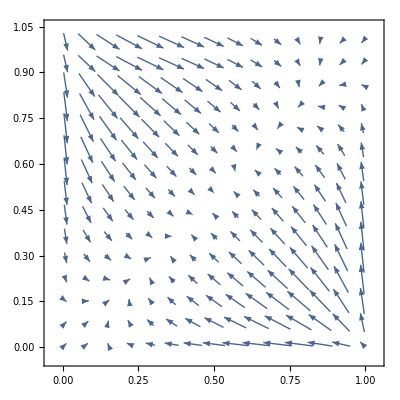

```mathematica
(* Plot -----------------------------------------------------------------------------------*)
(* Observations: the agent with greater alpha seems to be setting the dynamics (changing the other agent's parameters don't change anything) *)
(* Setting smaller gamma seems to be better *)
myPlot=VectorPlot[{X11next-X11/.Params,X21next-X21/.Params},{X11,0.01,0.99},{X21,0.01,1}]
(*Export["D:\\USB_send\\Project_Negotiation\\prospectiveporpoise\\beta1=0.5beta2=5.pdf",Style[myPlot,Magnification->1],ImageResolution->2000];*)
```

```mathematica
Params
```

{alpha1→0.1,alpha2→0.1,beta1→0.1,beta2→0.1,gamma1→0,gamma2→0,delta1→0.4,delta2→0}

```mathematica
(* Diffusion *)


Diff = X11*X21
```

X11 X21